I set a0 = 1 in calculations (, an implicit choice made when making the axvec’s unit vectors).

### Constants

```mathematica
a0=410;(*Lattice constant in nm, if I ever need it*)
(*A-B sublattice vectors*)
a1vec={1,0};
a2vec={-1/2,Sqrt[3]/2};
a3vec={-1/2,-Sqrt[3]/2};
(*Lattice vectors*)
l1vec={3/2,Sqrt[3]/2};
l2vec={-3/2,Sqrt[3]/2};
ToaVecList={a1->a1vec,a2->a2vec,a3->a3vec};
ToLatVecList={l1->l1vec,l2->l2vec};
(*High symmetry points*)
kNearK={d*kx,d*ky+Pi*4/3/Sqrt[3]};(*d is a dummy variable for series expansion*)
kNearKVecList=Append[ToaVecList,k->kNearK];
G1vec={2*Pi/3,2*Pi/Sqrt[3]};
G2vec={-2*Pi/3,2*Pi/Sqrt[3]};
kxyList=k->{kx,ky};
kpolarlist={kx->q*Cos[ϕ],ky->q*Sin[ϕ]};
Table[G.l,{G,{G1vec,G2vec}},{l,{l1vec,l2vec}}]
```

{{2 π,0},{0,2 π}}

### Hamiltonian

```mathematica
fkhexI=1+Exp[-I*k.l1]+Exp[-I*k.l2];
fkhexII=Exp[-I*k.a1]+Exp[-I*k.a2]+Exp[-I*k.a3];
fkhexIIkxy=fkhexII/.ToaVecList/.kxyList;
Wkhex(*Wronskian of f(k)*)=-2*((Cos[k.(a1-a1)]+Cos[k.(a2-a1)]+Cos[k.(a3-a1)])*a1+(Cos[k.(a1-a2)]+Cos[k.(a2-a2)]+Cos[k.(a3-a2)])*a2+(Cos[k.(a1-a3)]+Cos[k.(a2-a3)]+Cos[k.(a3-a3)])*a3);
HhexII={{0,fkhexII},{fkhexII*,0}};
HhexIIkxy=Apart[Simplify[HhexII/.ToaVecList/.kxyList,Assumptions->{kx∈Reals,ky∈Reals}]];
MatrixForm[HhexIIkxy]
```

(0 | ⅇ^(-ⅈ kx)+ⅇ^((ⅈ kx)/2-1/2 ⅈ √3 ky)+ⅇ^((ⅈ kx)/2+1/2 ⅈ √3 ky)
ⅇ^(ⅈ kx)+ⅇ^(-(ⅈ kx)/2-1/2 ⅈ √3 ky)+ⅇ^(-(ⅈ kx)/2+1/2 ⅈ √3 ky) | 0)

```mathematica
fNearK=fkhexII/.kNearKVecList
Series[fNearK,{d,0,2}]
```

ⅇ^(-ⅈ d kx)+ⅇ^(-ⅈ (-(d kx)/2-1/2 √3 (d ky+(4 π)/(3 √3))))+ⅇ^(-ⅈ (-(d kx)/2+1/2 √3 (d ky+(4 π)/(3 √3))))

-3/2 ⅈ (kx-ⅈ ky) d-3/8 (kx+ⅈ ky)^2 d^2+O[d]^3

With the right unitary transformation W, the Hamiltonian can be made real, as expected from the C2T symmetry. Since C2 exchanges A and B sublattice, C2 is represented by σ_x, and W is given by the Takagi factorization of σ_x.

```mathematica
Wuni={{1,I},{1,-I}}/Sqrt[2];
Table[MatrixForm[W],{W,{Wuni,Wuni†}}]
MatrixForm[ComplexExpand[Wuni†.HhexIIkxy.Wuni]]
MatrixForm[Wuni.Wuniᵀ](*This should be Subscript[σ, x]*)
```

{(1/(√2) | ⅈ/(√2)
1/(√2) | -ⅈ/(√2)),(1/(√2) | 1/(√2)
-ⅈ/(√2) | ⅈ/(√2))}

(Cos[kx]+Cos[kx/2-(√3 ky)/2]+Cos[kx/2+(√3 ky)/2] | -Sin[kx]+Sin[kx/2-(√3 ky)/2]+Sin[kx/2+(√3 ky)/2]
-Sin[kx]+Sin[kx/2-(√3 ky)/2]+Sin[kx/2+(√3 ky)/2] | -Cos[kx]-Cos[kx/2-(√3 ky)/2]-Cos[kx/2+(√3 ky)/2])

(0 | 1
1 | 0)

### Eigenstates

I’m still trying to figure out how to visualize this - for the honeycomb lattice, the sublattice weight is the same everywhere, and I’m try to visualize the relative phase between site A and B.
Note how the orientation of the arrow is NOT the same one reciprocal lattice away - this is one of the (perhaps unintuitive) finding in the Wilson line paper.

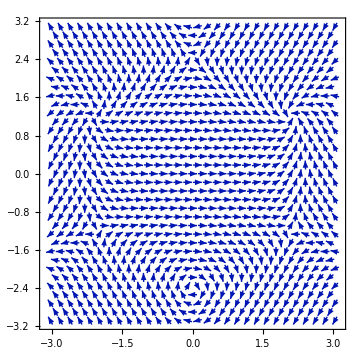
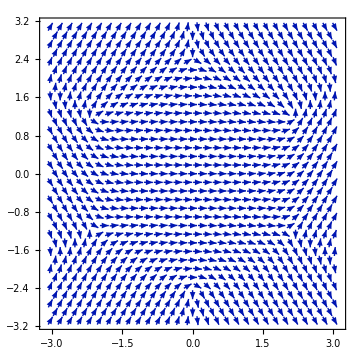

```mathematica
Subscript[ϕ, f]=Arg[fkhexIIkxy];
krange = Pi;
Table[VectorPlot[{Cos[Subscript[ϕ, f]/ph],Sin[Subscript[ϕ, f]/ph]},{kx,-krange,krange},{ky,-krange,krange},VectorPoints->30,ImageSize->Medium],{ph,{1,2}}]
```

### Berry Connection

```mathematica
A21IIraw=Wkhex/(4*Abs[fkhexII]^2);
A21simp1=FullSimplify[A21IIraw/.ToaVecList/.kxyList,Assumptions->{kx∈Reals,ky∈Reals}];
A21II=FullSimplify[ComplexExpand[A21simp1]]
```

{1/(4+(6 (1+2 Cos[(3 kx)/2] Cos[(√3 ky)/2]))/(-Cos[(3 kx)/2] Cos[(√3 ky)/2]+Cos[√3 ky])),-(√3 Sin[(3 kx)/2] Sin[(√3 ky)/2])/(6+8 Cos[(3 kx)/2] Cos[(√3 ky)/2]+4 Cos[√3 ky])}

```mathematica
Table[Plot3D[A21II[[idx]],{kx,-Pi,Pi},{ky,-Pi,Pi},PlotRange->{-5,5},MaxRecursion->6],{idx,{1,2}}]
```

{-Graphics3D-,-Graphics3D-}

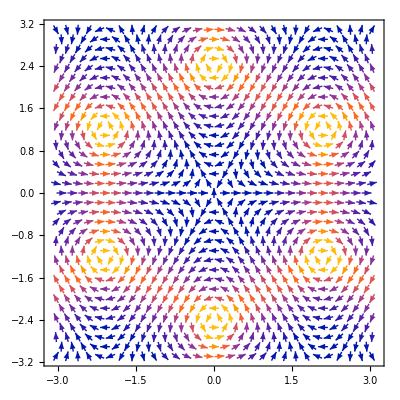

```mathematica
VectorPlot[A21II,{kx,-Pi,Pi},{ky,-Pi,Pi},VectorPoints->30]
```

```mathematica
A21IIMag=Sqrt[A21II[[1]]^2+A21II[[2]]^2];
Plot3D[A21IIMag,{kx,-Pi,Pi},{ky,-Pi,Pi},PlotRange->{0,4},MaxRecursion->6,MeshFunctions->{#3&},Mesh->10, AxesLabel->Automatic]
```

-Graphics3D-

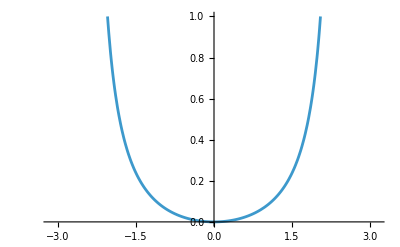
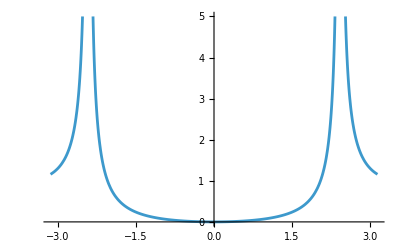

```mathematica
Table[Plot[A21IIMag/.kx->0,{ky,-Pi,Pi},PlotRange->{0,r}],{r,{1,5}}]
```

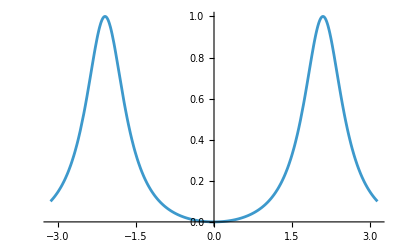
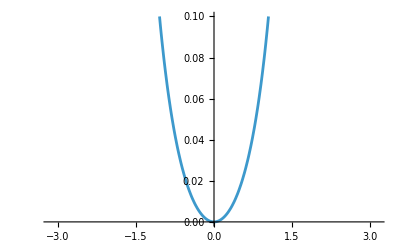

```mathematica
Table[Plot[A21IIMag/.ky->0,{kx,-Pi,Pi},PlotRange->{0,r}],{r,{1,0.1}}]
```

```mathematica
TranspLineEqn=Normal[Series[A21II.{Cos[θ],Sin[θ]}/.kpolarlist,{q,0,2}]]
Solve[TranspLineEqn==0,ϕ,Assumptions->θ∈Reals]
```

1/16 q^2 Cos[θ+2 ϕ]

{{ϕ→ConditionalExpression[1/2 (-π/2-θ+2 π C[1]), C[1]∈ℤ]},{ϕ→ConditionalExpression[1/2 (π/2-θ+2 π C[1]), C[1]∈ℤ]}}

### Euler curvature

This should be zero. While the eigenstates changes throughout the BZ (i.e. the basis vectors at each k is different), they span the same Hilbert space. Euler curvature (I believe) measures how twisted the spanned space is.
I think you can think of “you need at least three bands to see nontrivial Euler class” as the embedding of a twisted strip in 3D.

```mathematica
Eu21II=Curl[A21II,{kx,ky}];
Simplify[Eu21II]
```

0

### Hellman-Feynman (Not working yet)

```mathematica
{Evalsraw,Evecsraw}=Eigensystem[HhexIIkxy];
HhexIIkxydkx=D[HhexIIkxy,kx];
HhexIIkxydky=D[HhexIIkxy,ky];
Evals=PowerExpand[FullSimplify[Evalsraw,Assumptions->{kx∈Reals,ky∈Reals}]]
Evecs=PowerExpand[FullSimplify[Evecsraw,Assumptions->{kx∈Reals,ky∈Reals}]]
```

{-√(3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky]),√(3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])}

{{-(ⅇ^(-(ⅈ kx)/4+1/4 ⅈ (3 kx+2 √3 ky)) √(3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky]))/(1+ⅇ^(ⅈ √3 ky)+ⅇ^(1/2 ⅈ (3 kx+√3 ky))),1},{(ⅇ^(-(ⅈ kx)/4+1/4 ⅈ (3 kx+2 √3 ky)) √(3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky]))/(1+ⅇ^(ⅈ √3 ky)+ⅇ^(1/2 ⅈ (3 kx+√3 ky))),1}}

```mathematica
temp=I*Evecs[[2]].HhexIIkxydkx.Evecs[[1]]/(Evals[[2]]-Evals[[1]])
FullSimplify[temp,Assumptions->{kx∈Reals,ky∈Reals}]
1/Simplify[1/FullSimplify[temp,Assumptions->{kx∈Reals,ky∈Reals}]]
```

(ⅈ (-((ⅇ^(-(ⅈ kx)/4+1/4 ⅈ (3 kx+2 √3 ky)) (ⅈ ⅇ^(ⅈ kx)-1/2 ⅈ ⅇ^(-(ⅈ kx)/2-1/2 ⅈ √3 ky)-1/2 ⅈ ⅇ^(-(ⅈ kx)/2+1/2 ⅈ √3 ky)) √(3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky]))/(1+ⅇ^(ⅈ √3 ky)+ⅇ^(1/2 ⅈ (3 kx+√3 ky))))+(ⅇ^(-(ⅈ kx)/4+1/4 ⅈ (3 kx+2 √3 ky)) (-ⅈ ⅇ^(-ⅈ kx)+1/2 ⅈ ⅇ^((ⅈ kx)/2-1/2 ⅈ √3 ky)+1/2 ⅈ ⅇ^((ⅈ kx)/2+1/2 ⅈ √3 ky)) √(3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky]))/(1+ⅇ^(ⅈ √3 ky)+ⅇ^(1/2 ⅈ (3 kx+√3 ky)))))/(2 √(3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky]))

(ⅇ^(1/2 ⅈ (kx+√3 ky)) (Cos[kx]-Cos[kx/2] Cos[(√3 ky)/2]))/(1+ⅇ^(ⅈ √3 ky)+ⅇ^(1/2 ⅈ (3 kx+√3 ky)))

(ⅇ^(1/2 ⅈ (kx+√3 ky)) (Cos[kx]-Cos[kx/2] Cos[(√3 ky)/2]))/(1+ⅇ^(ⅈ √3 ky)+ⅇ^(1/2 ⅈ (3 kx+√3 ky)))